# Draw pictures for REED.tex on betweenness

```mathematica
dir=SetDirectory[NotebookDirectory[]];
NotebookEvaluate[dir<>"/lib/pow-reed.nb"]
```

Replicate  edges x -> y if x or y in groups

```mathematica
nameExpand=Map[("name"->"nodes")/.#&,groups];expandRule[u_->v_]:=Module[{ul=u/.nameExpand,vl=v/.nameExpand},
Outer[Rule,If[Head[ul]===List,ul,{ul}],If[Head[vl]===List,vl,{vl}]]
]
expandedEdges=Flatten@Map[expandRule,edges]
```

```mathematica
g=Graph@expandedEdges
```

```mathematica
vlist=VertexList[expandedEdges]
```

```mathematica
Thread[vlist-> b]
```

Show how much has been written for each node :

```mathematica
HighlightGraph[g,vlist,VertexSize->Thread[vlist-> Rescale[b]]]
```

```mathematica
bg=Map[Module[{b,g,max,maxi,vlist},
b=BetweennessCentrality[g=Subgraph[expandedEdges,#]];
max=Max[b];
If[Length[Position[b,max]]==1,
maxi=Position[b,max][[1,1]];
vlist=VertexList[g];
Print[vlist[[maxi]]/.vertexNames];
vlist=vlist/.vlist[[maxi]]->Style[vlist[[maxi]],Darker[Red]];
Print[vlist];
];
Print[b^2];
HighlightGraph[g,vlist,VertexSize-> Thread[VertexList[g]-> Rescale[b^.9]],
VertexLabels->{"7"->Placed[Style["PrecisionWeb\ndatabase",20,Bold,Black],{-1.2,-.5}]}]
]&,WeaklyConnectedComponents[expandedEdges]];
```

```mathematica
betweennessplot=Show[{Show[bg[[1]],ImageSize->1000],Show[bg[[2]],ImageSize->50]}]
```

```mathematica
Export["../REED-paper/figures/betweenness.png",betweennessplot]
```

## Now try and infer relations between highlights and keyword

A keyword implies a color if all nodes with that keyword have that color
A color implies a keyword if all nodes with that color have that keyword
A color and keyword are equivalent if the color implies the keyword and the keyword implies the color

```mathematica
allnodes=Union@Flatten[edges/.Rule->List]
```

```mathematica
allhighlights=Union[highlights/.(_->color_)->color]
```

```mathematica
allkeywords=Union@Flatten[Union[keywords/.(_->keyword_)->keyword]]
```

```mathematica
generalisedKeywords=Append[keywords,_->{}]
```

```mathematica
highlightof[node_]:=node/.highlights;
keywordsof[node_]:=node/.generalisedKeywords;
highlightednodes[color_]:=Cases[{#,highlightof@#}&/@allnodes,{node_,color}->node];
keywordednodes[keyword_]:=DeleteCases[Map[Module[{},
If[MemberQ[keywordsof[#],keyword],#,{}]
]&,allnodes],{}]
highlightof/@keywordednodes["Audit"]
```

```mathematica
highlightednodes["yellow"]
```

Find intersection of keywords for all nodes of highlight h

```mathematica
highlightof/@allnodes
```

```mathematica
ColumnForm@DeleteCases[Map[Implies[#,Intersection@@Map[keywordsof,highlightednodes[#]]]&,allhighlights],Implies[_,{}]]
```

```mathematica
ColumnForm@DeleteCases[Map[Implies[#,Intersection@@List/@Map[highlightof,keywordednodes[#]]]&,allkeywords],Implies[_,{}]]
```

```mathematica
keywordednodes["Corruption of evidence"]
```

```mathematica
{"Abbott_engineer"}
```

```mathematica
keywordsof/@%
```

```mathematica
keywordednodes["PrecisionWeb database"]
```

```mathematica
Print["=end-"]
```

```mathematica
HighlightGraph[,vlist,VertexSize->Thread[vlist->Rescale[b]]]
```

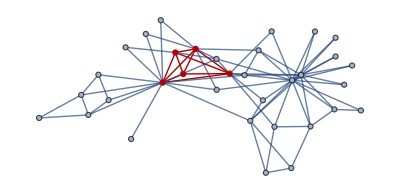

```mathematica
g=ExampleData[{"NetworkGraph","ZacharyKarateClub"}];
clique=FindClique[g];
plot=HighlightGraph[g, Subgraph[g,clique]];
Export["plot.pdf",plot]
```